### 1.自由落体运动

#### 求解微分方程

```mathematica
sol=DSolve[{x'[t]==v[t],v'[t]==-g-b/m v[t],x[0]==h,v[0]==v0},{x[t],v[t]},t]//ExpandAll
```

{{v[t]→-(g m)/b+(ⅇ^(-(b t)/m) g m)/b+ⅇ^(-(b t)/m) v0,x[t]→h+(g m^2)/b^2-(ⅇ^(-(b t)/m) g m^2)/b^2-(g m t)/b+(m v0)/b-(ⅇ^(-(b t)/m) m v0)/b}}

#### 终端速度

```mathematica
First[Flatten[sol]]/.(b t)/m->Infinity
```

v[t]→-(g m)/b

```mathematica
Flatten[sol][[1]]/.(b t)/m->Infinity
```

v[t]→-(g m)/b

#### 单位选取

```mathematica
vv[t_]=(v[t]/.Flatten[sol][[1]])//.{g m/b->1,b/m->1}
```

-1+ⅇ^-t+ⅇ^-t v0

#### 速度图像

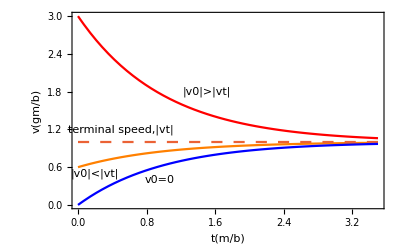

```mathematica
Plot[Evaluate[{Abs[vv[t]]/.v0->-3,Abs[vv[t]]/.v0->-0.6,Abs[vv[t]]/.v0->0 ,1}],{t,0,3.5},PlotRange->All,Frame->True,FrameLabel->{"t(m/b)","v(gm/b)"},PlotStyle->{{Red},{Orange},{Blue},{Dashing[{0.02}]}},Prolog->{Text["v0=0",{0.95,0.4}],Text["|v0|<|vt|",{0.2,0.5}],Text["|v0|>|vt|",{1.5,1.8}],Text["terminal speed,|vt|",{0.5,1.2}]}]
```

### 2.抛物运动

```mathematica
ClearAll["Global`*"]
projectile[v0_/;0<v0≤80,θ0_/;30<θ0≤85]:=Module[
{k=5.2 10^-3,g=9.81,vx0,vy0,x,y,R,H,tmax,T,pathWithoutAirResistance,sol,tab},
vx0=v0 Cos[θ0/180*Pi]//N;
vy0=v0 Sin[θ0/180*Pi]//N;
R=(2 vx0 vy0)/g;
H=vy0^2/(2g);
T=(2 vy0)/g;
pathWithoutAirResistance=Plot[vy0/vx0 x-1/2 g/vx0^2 x^2,{x,0,R},PlotRange->{0,H}];
sol=NDSolve[{x''[t]==-k √(x'[t]^2+y'[t]^2)x'[t],y''[t]==-k √(x'[t]^2+y'[t]^2)y'[t]-g,x[0]==0,y[0]==0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,T}];
x[t_]=x[t]/.sol[[1,1]];
y[t_]=y[t]/.sol[[1,2]];
tmax=t/.FindRoot[y[t],{t,T}];
tab=Table[
Show[
pathWithoutAirResistance,Graphics[{AbsolutePointSize[7],Red,Point[{x[(tmax/32)i],y[(tmax/32)i]}]}],ParametricPlot[{x[t],y[t]},{t,0,(tmax/32)i+0.0001},PlotStyle->{Blue,Dashing[{0.02,0.02}]}],PlotRange->{{-0.01,R},{-0.01,1.02H}},ImageSize->1000,LabelStyle->{FontSize->36},AxesLabel->{"x(m)","y(m)",AspectRatio->Automatic}],{i,0,32}];
Export[NotebookDirectory[]<>"projectile.gif",tab];
ListAnimate[tab]
];
```

```mathematica
projectile[45,60]
```

### 3. 钟摆运动

#### 有效势

```mathematica
effectivePotential[θ0_/;0≤θ0≤180,θdot0_,φdot0_,opts___Rule]:=
Module[{pφ},
pφ=Sin[θ0/180 Pi]^2 φdot0;
Plot[{1/2 pφ^2/Sin[θ/180 Pi]^2+Cos[θ/180 Pi],1/2(θdot0^2+pφ^2/Sin[θ0/180 Pi]^2)+Cos[θ0/180 Pi]},{θ,0+10^-3,180-10^-3},Ticks->{{0,90,180},Automatic},AxesLabel->{"θ(°)","U(mgR)"},PlotStyle->{{Thickness[0.0075]},{Dashing[{0.05,0.05}]}},opts]
]
```

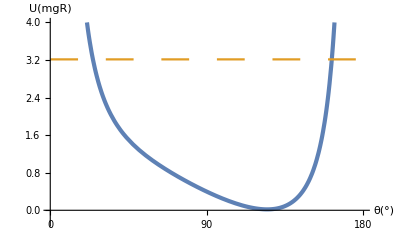

```mathematica
effectivePotential[135,2.5,1.5 2^(1/4),PlotRange->{-0.25,4}]
```

#### 运动方程

```mathematica
ClearAll["Global`*"];
sphericalPendulum[θ0_/;0≤θ0≤180,θdot0_/;Abs[θdot0]<10,φ0_/;0≤φ0≤360,φdot0_/;Abs[φdot0]<10,tmax_/;1≤tmax≤60,nv_Integer:999,opts___Rule]:=
Module[{n=nv,pφ,sol,θ,φ,x,y,z,sphere},
If[n>1,
If[n==999,n=Round[3 tmax]];
pφ=(Sin[θ0 °]^2 φdot0)//N;
sol=NDSolve[{θ''[t]-Cos[θ[t]]/Sin[θ[t]]^3 pφ^2-Sin[θ[t]]==0,φ'[t]==pφ/Sin[θ[t]]^2,θ[0]==θ0 °,θ'[0]==θdot0,φ[0]==φ0 °},{θ,φ},{t,0,tmax+0.01},
MaxSteps->6000];
θ=θ/.sol[[1,1]];
φ=φ/.sol[[1,2]];
x[t_]:=Sin[θ[t]]Cos[φ[t]];
y[t_]:=Sin[θ[t]]Sin[φ[t]];
z[t_]:=Cos[θ[t]];
sphere=ParametricPlot3D[{{0,Sin[t],Cos[t]},{Sin[t],0,Cos[t]}},{t,0,2Pi},
PlotStyle->{LineColor->Gray}];
tab=Table[Show[sphere,
Graphics3D[{Gray,Line[{{0,0,-1},{0,0,1}}]}],
ParametricPlot3D[{x[t],y[t],z[t]},{t,0,(tmax/(n-1))i+0.0001},
PlotStyle->{LineColor->Orange},
PlotPoints->(25+Round[12 tmax/(n-1)i])],
Graphics3D[{Thickness[0.0125],Red,Line[{{0,0,0},{x[(tmax/(n-1))i],y[(tmax/(n-1))i],z[(tmax/(n-1))i]}}],
PointSize[0.04],Red,Point[{x[(tmax/(n-1))i],y[(tmax/(n-1))i],z[(tmax/(n-1))i]}]}],
PlotRange->{{-1.25,1.25},{-1.25,1.25},{-1.25,1.25}},
BoxRatios->{1,1,1},
opts,
AxesLabel->{"x(R)","y(R)","z(R)"}],{i,0,n-1}];
Export[NotebookDirectory[]<>"sphericalPendulum.gif",tab];
ListAnimate[tab]
]
]
```

```mathematica
sphericalPendulum[120,0,45,0,13.6,Background->RGBColor[0.640004,0.580004,0.5]]
```

### 4. 电场

#### 矢量图

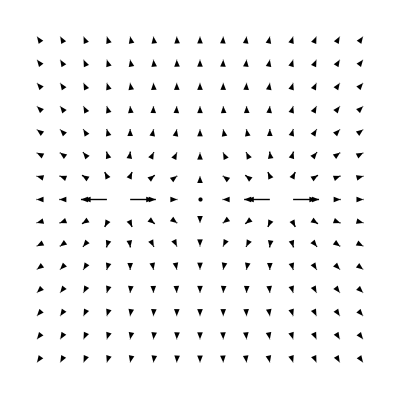

```mathematica
Needs["VectorFieldPlots`"]
GradientFieldPlot[-1/(√((x+1)^2+y^2))- 1/(√((x-1)^2+y^2)),{x,-2,2},{y,-2,2}]
```

#### 电场线与等势线

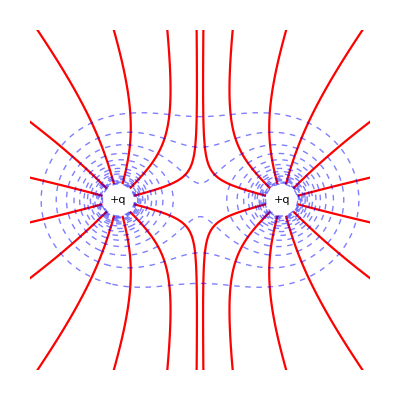

```mathematica
φ[x_,y_]:=1/(√((x+1)^2+y^2))+ 1/(√((x-1)^2+y^2));
EF[x_,y_]:=Evaluate[-∇_{x,y} φ[x,y]];
ℰ[x_,y_]:=Norm[EF[x,y]];
f[{x_,y_}]:={x,y}+0.02 EF[x,y]/ℰ[x,y];
x0[n_]:=N[-1+0.2Cos[(n π)/12]];
y0[n_]:=N[0.2Sin[(n π)/12]];
g[{x_,y_}]:=FixedPointList[f,{x,y},SameTest->((Norm[#2]>3)||(#2[[1]]>0)&)];
g/@Table[{x0[n],y0[n]},{n,1,11,2}];
coordinates1=Join[%,%/.{x_,y_}->{x,-y},%/.{x_,y_}->{-x,y},%/.{x_,y_}->{-x,-y}];
SetOptions[ListLinePlot,PlotStyle->Red];
Show[
ListLinePlot/@coordinates1,
ContourPlot[φ[x,y],{x,-2,2},{y,-2,2},
ContourShading->False,
PlotRange->{1.1,6.0},
Contours->16,
PlotPoints->50,
Frame->False,
ContourStyle->{{Blue,Dashing[{0.01,0.01}]}}],
Graphics[{Text["+q",{-1,0}],Text["+q",{1,0}]}],
AspectRatio->Automatic,
PlotRange->{{-2,2},{-2,2}},
Axes->False
]
```

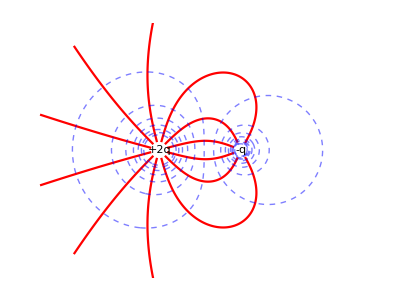

```mathematica
φ[x_,y_]:=2/(√((x+1)^2+y^2))+ -1/(√((x-1)^2+y^2));
EF[x_,y_]:=Evaluate[-∇_{x,y} φ[x,y]];
ℰ[x_,y_]:=Norm[EF[x,y]];
f[{x_,y_}]:={x,y}+0.02 EF[x,y]/ℰ[x,y];
x0[n_]:=N[-1+0.2Cos[(n π)/12]];
y0[n_]:=N[0.2Sin[(n π)/12]];
g[{x_,y_}]:=FixedPointList[f,{x,y},SameTest->((Norm[#2]>4)||EuclideanDistance[#2,{1,0}]≤0.2&)];
g/@Table[{x0[n],y0[n]},{n,1,11,2}];
coordinates2=Join[%,%/.{x_,y_}->{x,-y}];
SetOptions[ListLinePlot,PlotStyle->Red];
Show[
ListLinePlot/@coordinates2,
ContourPlot[φ[x,y],{x,-4,4},{y,-3,3},
ContourShading->False,
PlotRange->{-6,6.0},
Contours->16,
PlotPoints->50,
Frame->False,
ContourStyle->{{Blue,Dashing[{0.01,0.01}]}}],
Graphics[{Text["+2q",{-1,0}],Text["-q",{1,0}]}],
AspectRatio->Automatic,
PlotRange->{{-4,4},{-3,3}},
Axes->False
]
```

### 5. 带电粒子在电磁场下运动

```mathematica
ClearAll["Global`*"];
r[t_]:={x[t],y[t],z[t]};
EF:={0,E0,0};
BF:={0,0,B0};
Thread/@{m r''[t]==q EF+q r'[t]×BF,r[0]=={0,0,0},r'[0]=={vx0,vy0,vz0}}//Flatten;
sol=DSolve[%,{x[t],y[t],z[t]},t]//.{B0->m ω/q,E0->vd B0}//Flatten//Simplify//ExpandAll;
eqn=sol/.Rule->Equal
```

{x[t]==t vd+vy0/ω-(vy0 Cos[t ω])/ω-(vd Sin[t ω])/ω+(vx0 Sin[t ω])/ω,y[t]==vd/ω-vx0/ω-(vd Cos[t ω])/ω+(vx0 Cos[t ω])/ω+(vy0 Sin[t ω])/ω,z[t]==t vz0}

```mathematica
Map[(#-(t vd+vy0/ω))^2&,eqn[[1]]];
Map[(#-(vd/ω-vx0/ω))^2&,eqn[[2]]];
Thread[Plus[%%,%],Equal];
MapAt[Simplify,%,2]
```

(-t vd-vy0/ω+x[t])^2+(-vd/ω+vx0/ω+y[t])^2==(vd^2-2 vd vx0+vx0^2+vy0^2)/ω^2

```mathematica
{x[t_],y[t_],z[t_]}={x[t],y[t],z[t]}/.sol;
```

```mathematica
g[i_]:=(vx0=i;
Show[
ParametricPlot3D[{x[t],y[t],0},{t,0,22}],
ParametricPlot3D[r[t],{t,0,22}],
Graphics3D[{Thickness[0.008],
Line[{{0,0,0},{0,0,5}}],
Line[{{0,0,0},{0,5,0}}],
Line[{{0,0,0},{22,0,0}}],
Text[Style["E",FontFamily->"Times",Bold,12],{1.3,5.5,0}],
Text[Style["B",FontFamily->"Times",Bold,12],{0,0,7}],
Text[Style["v_x0="<>ToString[vx0],FontFamily->"Times",12],Scaled[{0.4,0.9,0.85}]]
}],
Axes->False,PlotRange->{{-2,24},{-7,7},{0,22}},ImageSize->140]
);
```

```mathematica
{ω,vd,vz0,vy0}={1,1,0.75,0};
Print["\nω = ",ω," v_d = ",vd," v_z0 = ",vz0," v_y0 = ",vy0,"\n"];
Grid[Partition[Table[g[i],{i,-1,4}],3],Spacings->{1.5,2.0}]
```

ω = 1 v_d = 1 v_z0 = 0.75 v_y0 = 0

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
motion[parms_]:=({ω,vd,vx0,vy0,vz0}=parms;
ListAnimate[
Table[Show[
ParametricPlot3D[r[t],{t,0,i+0.0001}],
Graphics3D[{Thickness[0.008],
Line[{{0,0,0},{0,0,5}}],
Line[{{0,0,0},{0,5,0}}],
Line[{{0,0,0},{24,0,0}}],
Text[Style["E",FontFamily->"Times",Bold,12],{1.3,5.5,0}],
Text[Style["B",FontFamily->"Times",Bold,12],{0,0,7}],
{Dashing[{0.01,0.01}],Line[{r[i],{x[i],y[i],0}}]},
{PointSize[0.03],Point[r[i]],GrayLevel[0.55],Point[{x[i],y[i],0}]}
}],
Axes->False,PlotRange->{{-2,25},{-7,7},{0,22}}
],{i,0,25}]
])
```

```mathematica
motion[{1,1,4,0,0.75}]
```

```mathematica
motion[{1,1,0,4,0.75}]
```

```mathematica
motion[{1,1,2,2,0.75}]
```

### 6. 粒子在中心力场中的运动

```mathematica
Get[NotebookDirectory[]<>"CoulombPotential.wl"]
```

```mathematica
Plot[{WaveR[1,ρ,1,0],WaveR[1,ρ,2,0],WaveR[1,ρ,3,0],WaveR[1,ρ,4,0]},{ρ,0,35},AxesLabel->{"ρ","R(ρ)"},Prolog->Thickness[0.001],PlotRange->{-0.2,0.2},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
Plot[{WaveR[1,ρ,3,2],WaveR[1,ρ,4,2],WaveR[1,ρ,5,2],WaveR[1,ρ,6,2]},{ρ,0,35},AxesLabel->{"ρ","R(ρ)"},Prolog->Thickness[0.001],PlotRange->{-0.02,0.02},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
Grid[Partition[Table[Plot3D[Abs[WaveA[theta,phi,2,i]]^2,{theta,0,Pi},{phi,0,2Pi},AxesLabel->{"θ","φ","|Y|^2"},PlotLabel->Style["m="<>ToString[i],Red,Bold,20],ImageSize->300],{i,0,3}],2]]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

```mathematica
Grid[Partition[Table[Plot3D[Abs[WaveF[1,ρ,theta,Pi/2,num[[1]],num[[2]],num[[3]]]]^2,{ρ,0,15},{theta,0,Pi},AxesLabel->{"ρ","θ","|ψ|^2"},Lighting->True,PlotLabel->Style["n="<>ToString[num[[1]]]<>",l="<>ToString[num[[2]]]<>",m="<>ToString[num[[3]]],Red,Bold,20],ImageSize->300],{num,{{3,0,0},{3,2,2},{3,2,0},{3,1,1}}}],2]]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

### 7. 非相对论性薛定谔方程本征能量限

#### 变分法

#### Ĥ=-∇^2/(2μ)+ar^n

##### 选取氢原子基态波函数作为试探函数，计算期望值

```mathematica
ψ[r_,λ_]=λ^(3/2)/(√π)ⅇ^(- λ r);
g[r_,λ_]=D[ψ[r,λ], r,r]+2/r D[ψ[r,λ], r];
(*T*)-1/(2μ)4π∫_0^∞ ψ[r,λ]g[r,λ] r^2 ⅆr
(*V*) 4π∫_0^∞ ψ[r,λ]a r^n ψ[r,λ] r^2 ⅆr
```

ConditionalExpression[λ^2/(2 μ),Re[λ]>0]

ConditionalExpression[2^(-1-n) a λ^-n Gamma[3+n],Re[n]>-3&&Re[λ]>0]

所以
E(λ)=λ^2/(2 μ)+2^(-1-n) a λ^-n Γ(3+n)=λ^2/(2 μ)+a/2(Γ(n+3))/(2λ)^n

##### 求最小值

```mathematica
𝔼[λ_]:=λ^2/(2 μ)+a/2 Gamma[n+3]/(2λ)^n;
Solve[D[𝔼[λ], λ]==0,λ]
𝔼[λ]/.%[[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{λ→(2^(-1-n) a n μ Gamma[3+n])^(1/(2+n))}}

((2^(-1-n) a n μ Gamma[3+n])^(2/(2+n)))/(2 μ)+2^(-1-n) a Gamma[3+n] ((2^(-1-n) a n μ Gamma[3+n])^(1/(2+n)))^-n

#### 线性势

##### 验证正交性

```mathematica
psi0[λ_,r_]:=λ^(3/2)/(√π)ⅇ^(-λ r);
psi1[λ_,r_]:=λ^(3/2)/(√(3π))(3-2λ r)ⅇ^(-λ r);
4π∫_0^∞ psi0[λ,r]psi1[λ,r] r^2 ⅆr
```

ConditionalExpression[0,Re[λ]>0]

##### 哈密顿量期望矩阵

```mathematica
psi[λ_,r_]:=({{psi0[λ,r]}, {psi1[λ,r]}});
"定义径向哈密顿算子";
H[psi_]:=-1/(2μ)(D[psi, r,r]+2/r D[psi, r])+a r psi;
psi[λ,r].H/@psi[λ,r]ᵀ//Simplify//MatrixForm
HM[λ_,a_,μ_]=Simplify[4π ∫_0^∞ %r^2 ⅆr//ExpandAll,λ>0];
HM[λ,a,μ]//MatrixForm
```

((ⅇ^(-2 r λ) λ^3 (2 λ-r λ^2+2 a r^2 μ))/(2 π r μ) | (ⅇ^(-2 r λ) λ^3 (-11 r λ^2+2 r^2 λ^3+6 a r^2 μ+λ (10-4 a r^3 μ)))/(2 √3 π r μ)
(ⅇ^(-2 r λ) λ^3 (-3+2 r λ) (-2 λ+r λ^2-2 a r^2 μ))/(2 √3 π r μ) | (ⅇ^(-2 r λ) λ^3 (-3+2 r λ) (11 r λ^2-2 r^2 λ^3-6 a r^2 μ+2 λ (-5+2 a r^3 μ)))/(6 π r μ))

((λ^3+3 a μ)/(2 λ μ) | (2 λ^3-3 a μ)/(2 √3 λ μ)
(2 λ^3-3 a μ)/(2 √3 λ μ) | (5 a)/(2 λ)+(7 λ^2)/(6 μ))

##### 求矩阵本征值和能量本征值估计

```mathematica
Eigenvalues[HM[λ,a,μ]]
```

{(5 λ^3+12 a μ-2 √(4 λ^6-6 a λ^3 μ+9 a^2 μ^2))/(6 λ μ),(5 λ^3+12 a μ+2 √(4 λ^6-6 a λ^3 μ+9 a^2 μ^2))/(6 λ μ)}

```mathematica
Eigenvalues[HM[1,1,1/2]]
%//N
```

{1/3 (11+√13),1/3 (11-√13)}

{4.86852,2.46482}

##### 基态

```mathematica
FindMinimum[Eigenvalues[HM[λ,1,1/2]][[1]],{λ,0.5}]
```

{2.35344,{λ→1.4561}}